```mathematica
Remove[r,theta,x1,x2,mu,omega,sol,sol1,eq1,eq2,T,r0]
sol = Solve[{mu*r==r^3},{r}]

r0 = r/.sol[[3]]

thetaP = omega+nu*r0^2;
T = 2*Pi/(thetaP)

x1 = r*Cos[theta];
x2=r*Sin[theta];
Remove[thetaP,rP,omega,nu,mu]

eq1 = rP*Cos[theta]-r*Sin[theta]*thetaP == 1/10*x1-x2^3-x1*x2^2-x1^2*x2-x2-x1^3;
eq2 = rP*Sin[theta]+r*Cos[theta]*thetaP == x1+1/10*x2+x1*x2^2+x1^3-x2^3-x1^2*x2;
sol1 = Solve[{eq1,eq2},{rP,thetaP}];

rP = rP/.sol1[[1]]
thetaP = thetaP/.sol1[[1]]

{mu,omega,nu} = {1/10,1,1}
```

{{r→0},{r→-√mu},{r→√mu}}

√mu

(2 π)/(mu+omega)

1/10 (r-10 r^3 Cos[theta]^2-10 r^3 Sin[theta]^2)

1+r^2 Cos[theta]^2+r^2 Sin[theta]^2

{1/10,1,1}

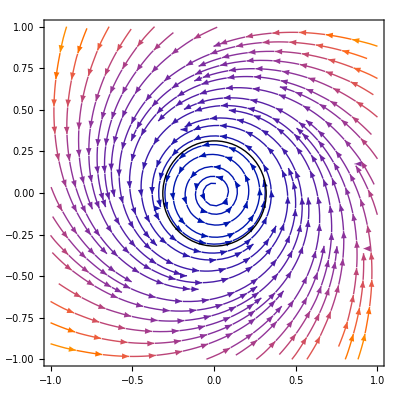

```mathematica
Remove[r,theta,x1,x2,mu,omega,t]
x1'[t] = 1/10*x1[t]-x2 [t]^3-x1[t]*x2[t]^2-x1[t]^2*x2[t]-x2[t]-x1[t]^3;
x2'[t] = x1[t]+1/10*x2[t]+x1[t]*x2[t]^2+x1[t]^3-x2[t]^3-x1[t]^2*x2[t];

Show[
StreamPlot[{1/10*x1[t]-x2 [t]^3-x1[t]*x2[t]^2-x1[t]^2*x2[t]-x2[t]-x1[t]^3,x1[t]+1/10*x2[t]+x1[t]*x2[t]^2+x1[t]^3-x2[t]^3-x1[t]^2*x2[t]},{x1[t],-1,1},{x2[t],-1,1}],
Graphics[Circle[{0,0},Sqrt[1/10]]]
]
```

{{0.316228},{-6.71405×10^-9},{0.319053},{2.12317×10^-8},{0.680947},{1.}}

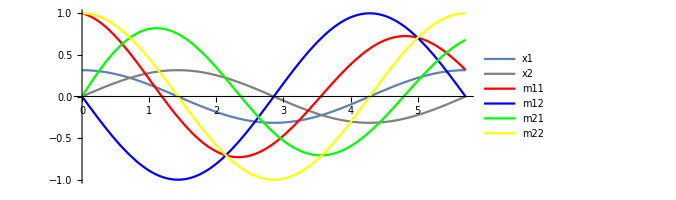

{{0.319053,2.12317×10^-8},{0.680947,1.}}

{1.,0.319053}

5.78753×10^-9

-0.2

```mathematica
Remove[x1,x2,m11,m21,m22,m12]
T=2*Pi/1.1;
s=NDSolve[{x1'[t]== x1[t]/10-x2[t]^3-x1[t]*x2[t]^2-x1[t]^2*x2[t]-x2[t]-x1[t]^3,
			x2'[t]==x1[t]+x2[t]/10+x1[t]*x2[t]^2+x1[t]^3-x2[t]^3-x1[t]^2*x2[t],
			m11'[t]==m11[t]*(1/10-x2[t]^2-2*x1[t]*x2[t]-3*x1[t]^2)+
				 m21[t]*(-3x2[t]^2-2*x1[t]*x2[t]-x1[t]^2-1),
			m12'[t]==m12[t]*(1/10-x2[t]^2-2*x1[t]*x2[t]-3*x1[t]^2)+
				 m22[t]*(-3x2[t]^2-2*x1[t]*x2[t]-x1[t]^2-1),
			m21'[t]==m11[t]*(1+x2[t]^2+3*x1[t]^2-2x1[t]*x2[t])+
			      m21[t]*(1/10+2*x1[t]*x2[t]-3x2[t]^2-x1[t]^2),
			m22'[t]==m12[t]*(1+x2[t]^2+3*x1[t]^2-2x1[t]*x2[t])+
			      m22[t]*(1/10+2*x1[t]*x2[t]-3x2[t]^2-x1[t]^2),
			x1[0]==Sqrt[0.1],x2[0]==0,m11[0]==1,m12[0]==0,m21[0]==0,m22[0]==1},{x1,x2,m11,m12,m21,m22},{t,0,T}];
{x1[T]/.s,x2[T]/.s,m11[T]/.s,m12[T]/.s,m21[T]/.s,m22[T]/.s}

Show[ParametricPlot[Evaluate[{t,x1[t]}/. s],{t,0,T},PlotLegends->{x1}],
ParametricPlot[Evaluate[{t,x2[t]}/. s],{t,0,T},PlotStyle->Gray,PlotLegends->{x2}],
ParametricPlot[Evaluate[{t,m11[t]}/. s],{t,0,T},PlotStyle->Red,PlotLegends->{m11}],
ParametricPlot[Evaluate[{t,m12[t]}/. s],{t,0,T},PlotStyle->Blue,PlotLegends->{m12}],
ParametricPlot[Evaluate[{t,m21[t]}/. s],{t,0,T},PlotStyle->Green,PlotLegends->{m21}],
ParametricPlot[Evaluate[{t,m22[t]}/. s],{t,0,T},PlotStyle->Yellow,PlotLegends->{m22}],
PlotRange->All
]

M = {{m11[T]/.s[[1]],m12[T]/.s[[1]]},{m21[T]/.s[[1]],m22[T]/.s[[1]]}}
lambda = Eigenvalues[M]
Log[lambda[[1]]]/T
Log[lambda[[2]]]/T
```